```mathematica
SetDirectory[NotebookDirectory[]];
<<qi.m;
```

SetDelayed::write: Tag SquareMatrixQ in SquareMatrixQ[A_] is Protected.

Package QI version 0.4.37 (last modification: 21/12/2012).

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

```mathematica
Log1[x_]:=If[x==0,0,Log[x]];
MatrixLog1[X_]:=Module[{ss,S,IS,eigenV,eigenVmat},(ss=Eigenvectors[X];
S=Transpose[ss];IS=Inverse[S];eigenV=Eigenvalues[X];
eigenVmat=DiagonalMatrix[eigenV];
For[i=1,i<=Length[eigenV],i++, eigenVmat[[i]][[i]]=Log1[Re[eigenV[[i]]]]];
S.DiagonalMatrix[Diagonal[eigenVmat]].IS)]
Log11[x_]:= If[x==0,0,Log2[Abs[x]]];
VEntropy[x_]:= -(x Log11[x] + (1-x)Log11[1-x]);
```

```mathematica
comp[x_?NumericQ,y_?NumericQ]:= x +I y;
mkvec2[x01_?NumericQ,x02_?NumericQ,x03_?NumericQ,x04_?NumericQ,y01_?NumericQ,y02_?NumericQ,y03_?NumericQ,y04_?NumericQ]:={comp[x01,y01],comp[x02,y02],comp[x03,y03],comp[x04,y04]};
densmat[v_]:=ConjugateTranspose[{v}].{v};
densmat1[v_]:=Simplify[Expand[ConjugateTranspose[v].v]];
pdensmat1[M_]:=PartialTrace[M,{2,2,2,2},{2,4}];
pdensmat2[M_]:= PartialTrace[M,{2,2},{1}];
Clear[NEntropy];
NEntropy[M_]:=Expand[ Tr[-MatrixLog1[M].M]/Log[2]];
veckraus[a_,b_]:=KroneckerProduct[{a},{b}];
Clear[Finvec];
Finvec[ar_?NumericQ,br_?NumericQ,ai_?NumericQ,bi_?NumericQ,c01_?NumericQ,c02_?NumericQ,c03_?NumericQ,c04_?NumericQ,c11_?NumericQ,c12_?NumericQ,c13_?NumericQ,c14_?NumericQ,c21_?NumericQ,c22_?NumericQ,c23_?NumericQ,c24_?NumericQ,c31_?NumericQ,c32_?NumericQ,c33_?NumericQ,c34_?NumericQ,d01_?NumericQ,d02_?NumericQ,d03_?NumericQ,d04_?NumericQ,d11_?NumericQ,d12_?NumericQ,d13_?NumericQ,d14_?NumericQ,d21_?NumericQ,d22_?NumericQ,d23_?NumericQ,d24_?NumericQ,d31_?NumericQ,d32_?NumericQ,d33_?NumericQ,d34_?NumericQ,m1_?NumericQ,m2_?NumericQ,m3_?NumericQ,m4_?NumericQ]:=(m1)veckraus[mkvec2[Re[ar],0,0,Re[br],Re[ai],0,0,Re[bi]],mkvec2[Re[c01],Re[c02],Re[c03],Re[c04],Re[d01],Re[d02],Re[d03],Re[d04]]]+
(m2)veckraus[mkvec2[Re[br],0,0,-Re[ar],Re[bi],0,0,-Re[ai]],mkvec2[Re[c11],Re[c12],Re[c13],Re[c14],Re[d11],Re[d12],Re[d13],Re[d14]]]+(m3)veckraus[mkvec2[0,Re[ar],Re[br],0,0,Re[ai],Re[bi],0],mkvec2[Re[c21],Re[c22],Re[c23],Re[c24],Re[d21],Re[d22],Re[d23],Re[d24]]]+(m4)veckraus[mkvec2[0,Re[br],-Re[ar],0,0,Re[bi],-Re[ai],0],mkvec2[Re[c31],Re[c32],Re[c33],Re[c34],Re[d31],Re[d32],Re[d33],Re[d34]]];
Clear[Optm];
Optm[ar_?NumericQ,br_?NumericQ,ai_?NumericQ,bi_?NumericQ,c01_?NumericQ,c02_?NumericQ,c03_?NumericQ,c04_?NumericQ,c11_?NumericQ,c12_?NumericQ,c13_?NumericQ,c14_?NumericQ,c21_?NumericQ,c22_?NumericQ,c23_?NumericQ,c24_?NumericQ,c31_?NumericQ,c32_?NumericQ,c33_?NumericQ,c34_?NumericQ,d01_?NumericQ,d02_?NumericQ,d03_?NumericQ,d04_?NumericQ,d11_?NumericQ,d12_?NumericQ,d13_?NumericQ,d14_?NumericQ,d21_?NumericQ,d22_?NumericQ,d23_?NumericQ,d24_?NumericQ,d31_?NumericQ,d32_?NumericQ,d33_?NumericQ,d34_?NumericQ,m1_?NumericQ,m2_?NumericQ,m3_?NumericQ,m4_?NumericQ]:=Re[m1^2*NEntropy[pdensmat2[densmat[mkvec2[Re[c01],Re[c02],Re[c03],Re[c04],Re[d01],Re[d02],Re[d03],Re[d04]]]]]+m2^2*NEntropy[pdensmat2[densmat[mkvec2[Re[c11],Re[c12],Re[c13],Re[c14],Re[d11],Re[d12],Re[d13],Re[d14]]]]]+m3^2*NEntropy[pdensmat2[densmat[mkvec2[Re[c21],Re[c22],Re[c23],Re[c24],Re[d21],Re[d22],Re[d23],Re[d24]]]]]+m4^2*NEntropy[pdensmat2[densmat[mkvec2[Re[c31],Re[c32],Re[c33],Re[c34],Re[d31],Re[d32],Re[d33],Re[d34]]]]]-NEntropy[pdensmat1[densmat1[Finvec[ar,br,ai,bi,c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34,m1,m2,m3,m4]]]]];
```

```mathematica
NMaximize[{Optm[0.45,Sqrt[1-0.45^2],0,0,c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34,m1,m2,m3,m4],c01^2+c02^2+c03^2+c04^2+d01^2+d02^2+d03^2+d04^2==1&&c11^2+c12^2+c13^2+c14^2+d11^2+d12^2+d13^2+d14^2==1&&c31^2+c32^2+c33^2+c34^2+d31^2+d32^2+d33^2+d34^2==1&&c21^2+c22^2+c23^2+c24^2+d21^2+d22^2+d23^2+d24^2==1&&m1^2+m2^2+m3^2+m4^2==1},{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34,m1,m2,m3,m4}]
```

{6.6409×10^-9,{c01→-0.166066,c02→-0.111061,c03→0.179812,c04→0.591142,c11→-0.0392917,c12→0.417328,c13→0.558066,c14→-0.0185539,c21→-0.256586,c22→0.0977535,c23→-0.0122531,c24→0.0725627,c31→0.256586,c32→-0.0977534,c33→0.0122531,c34→-0.0725627,d01→0.0264529,d02→-0.497507,d03→0.545499,d04→0.180344,d11→-0.120798,d12→0.63922,d13→-0.287539,d14→0.0814832,d21→-0.041995,d22→0.0360253,d23→0.891886,d24→-0.347376,d31→0.0419949,d32→-0.0360252,d33→-0.891886,d34→0.347376,m1→-8.63222×10^-9,m2→-6.94071×10^-9,m3→0.49,m4→-0.871722}}

```mathematica
Optm[0.45,0.8930285549745876,0,0,0.23827063865985368,0.6100824936028095,0.3733996176838027,0.14542458286916368,-0.3447979279662202,0.22201139359399197,0.7506876183284843,0.7174314416740758,0.13768011930562385,0.3676959163411362,-0.640486685968459,0.2971419502343311,0.5229237029402284,0.57102552322792,-0.5244977225578553,0.2320045564106432,-0.3455506369756619,-0.6807904449892351,0.47574909563544177,-0.5631609724553858,-0.03902206350973818,0.4904705085982526,0.6894769556704217,-0.8337652383585231,0.9379461841579994,-0.7162141789930683,0.12251274248806274,0.2525567442225717,0.4778091353752214,-0.727217056301363,0.6289616869324343,-0.4502721762735431,-0.421235646157919,-0.030359527432598423]//N
MatrixLog1[{{0.5419426164460109+0. ⅈ,0.16699047760125854-0.23086768544140557 ⅈ},{0.16699047760125854+0.23086768544140557 ⅈ,1.173974869188829+0.ⅈ}}]//N
```

-2.75687

(-0.698318-1.73472×10^-18 ⅈ | 0.213463-0.295117 ⅈ
0.213463+0.295117 ⅈ | 0.109605+0. ⅈ)

```mathematica
m = 1;
FindMaximum[{VEntropy[c^2]-VEntropy[(m*c+Sqrt[1-m^2]*d)^2],c^2+d^2==1},{{c,1},{d,1}}]
```

{0.,{c→0.707108,d→0.707108}}

```mathematica
List2 = {}
For[ar=0.05,ar<1,ar = ar+0.05,List2=Append[List2,{VEntropy[ar^2],NMaximize[{Optm[ar,Sqrt[1-ar^2],0,0,c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34],c01^2+c02^2+c03^2+c04^2+d01^2+d02^2+d03^2+d04^2==1&&c11^2+c12^2+c13^2+c14^2+d11^2+d12^2+d13^2+d14^2==1&&c31^2+c32^2+c33^2+c34^2+d31^2+d32^2+d33^2+d34^2==1&&c21^2+c22^2+c23^2+c24^2+d21^2+d22^2+d23^2+d24^2==1},{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34},Method->"DifferentialEvolution"][[1]]}]]
```

{}

```mathematica
List2
```

{{0.0252119,0.13781},{0.0807931,0.274831},{0.155256,0.41025},{0.242292,0.543217},{0.33729,0.672813},{0.43647,0.798025},{0.536505,0.917705},{0.63431,1.03053},{0.7269,1.13493},{0.811278,1.229},{0.884325,1.31038},{0.942683,1.37603},{0.9826,1.42191},{0.999711,1.44233},{0.988699,1.42908},{0.942683,1.37603},{0.852022,1.27435},{0.701471,1.10642},{0.46102,0.827905}}

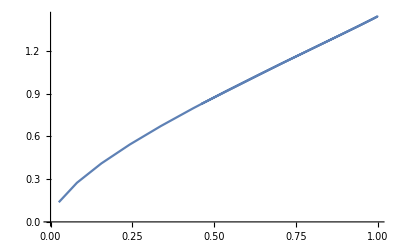

```mathematica
p2=ListLinePlot[List2]
```

```mathematica
NMaximize[{Optm[0.34,Sqrt[1-0.34^2],0,0,c01,0,0,c04,c04,0,0,-c01,0,c22,c23,0,0,c23,-c22,0,d01,0,0,d04,d04,0,0,-d01,0,d22,d23,0,0,d23,-d22,0,0.5,0.5,0.5,0.5],c01^2+c04^2+d01^2+d04^2==1&&c22^2+c23^2+d22^2+d23^2==1},{c01,c04,c22,c23,d01,d04,d22,d23},Method->"DifferentialEvolution"]
```

{0.619862,{c01→-0.885697,c04→0.4632,c22→0.885697,c23→-0.4632,d01→-0.0278353,d04→0.0145572,d22→0.0278353,d23→-0.0145573}}

```mathematica
List1 = {}
For[ar=0.05,ar<1,ar = ar+0.05,List1=Append[List1,{VEntropy[ar^2], NMaximize[{Optm[ar,Sqrt[1-ar^2],0,0,c01,0,0,c04,c04,0,0,-c01,0,c01,c04,0,0,c04,-c01,0,d01,0,0,d04,d04,0,0,-d01,0,d01,d04,0,0,d04,-d01,0],c01^2+c04^2+d01^2+d04^2==1},{c01,c04,d01,d04}][[1]]}]]
```

{}

{{0.0252119,0.0955229},{0.0807931,0.190498},{0.155256,0.284364},{0.242292,0.37653},{0.33729,0.466359},{0.43647,0.553148},{0.536505,0.636105},{0.63431,0.714309},{0.7269,0.786674},{0.811278,0.851881},{0.884325,0.908292},{0.942683,0.953793},{0.9826,0.985595},{0.999711,0.999747},{0.988699,0.990565},{0.942683,0.953794},{0.852022,0.883311},{0.701471,0.766915},{0.46102,0.57386}}

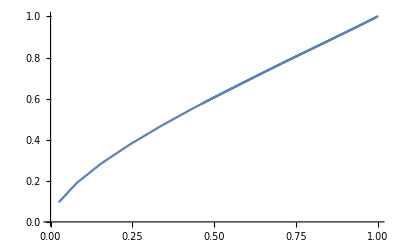

```mathematica
List1
p1=ListLinePlot[List1]
```

```mathematica
NMaximize[{Optm[0.45,Sqrt[1-0.45^2],0,0,c01,0,0,c04,c04,0,0,-c01,0,c01,c04,0,0,c04,-c01,0,d01,0,0,d04,d04,0,0,-d01,0,d01,d04,0,0,d04,-d01,0],c01^2+c04^2+d01^2+d04^2==1},{c01,c04,d01,d04}]
m = 0.45;
FindMaximum[{VEntropy[c^2]-VEntropy[(m*c+Sqrt[1-m^2]*d)^2],c^2+d^2==1},{{c,1},{d,1}}]
NMaximize[{Optm[0.45,Sqrt[1-0.45^2],0,0,c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34],c01^2+c02^2+c03^2+c04^2+d01^2+d02^2+d03^2+d04^2==1&&c11^2+c12^2+c13^2+c14^2+d11^2+d12^2+d13^2+d14^2==1&&c31^2+c32^2+c33^2+c34^2+d31^2+d32^2+d33^2+d34^2==1&&c21^2+c22^2+c23^2+c24^2+d21^2+d22^2+d23^2+d24^2==1},{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24,c31,c32,c33,c34,d01,d02,d03,d04,d11,d12,d13,d14,d21,d22,d23,d24,d31,d32,d33,d34},Method->"DifferentialEvolution"]
```

{0.786674,{c01→-0.815896,c04→0.50649,d01→0.236949,d04→-0.147093}}

{0.786674,{c→0.527417,d→0.849607}}

{0.786674,{c01→-0.0940458,c02→-0.410651,c03→-0.443188,c04→-0.311859,c11→0.418146,c12→-0.162782,c13→0.168453,c14→0.391448,c21→-0.14247,c22→0.31623,c23→-0.420132,c24→0.238389,c31→0.310161,c32→0.194901,c33→0.251285,c34→-0.284871,d01→0.507149,d02→0.150919,d03→-0.0797845,d04→0.49245,d11→0.269416,d12→-0.518281,d13→-0.505339,d14→0.143115,d21→0.576144,d22→-0.0722153,d23→0.0492272,d24→-0.553877,d31→0.195153,d32→0.6085,d33→-0.520958,d34→-0.204361}}

```mathematica
Sqrt[0.8158964260881677^2+0.23694906425631468^2]
NEntropy[pdensmat2[densmat[mkvec2[-0.09404582442332117,-0.41065128435791826,-0.4431879086514756,-0.31185859426917195,0.5071493598323493,0.15091890282451773,-0.07978445817852543,0.4924500504606095]]]]
(*f01=0.8;
f04=0.5064898004313906;
g01=0.2860626455086156;
g04=-0.14709265058357066;
Optm[0.45,Sqrt[1-0.45^2],0,0,f01,0,0,f04,f04,0,0,-f01,0,f01,f04,0,0,f04,-f01,0,g01,0,0,g04,g04,0,0,-g01,0,g01,g04,0,0,g04,-g01,0]*)
f01=0.8158964260881677;
f04=-0.5064898004313906;
g01=-0.23694906425631468;
g04=+0.14709265058357066;
Optm[0.45,Sqrt[1-0.45^2],0,0,f01,0,0,f04,f04,0,0,-f01,0,f01,f04,0,0,f04,-f01,0,g01,0,0,g04,g04,0,0,-g01,0,g01,g04,0,0,g04,-g01,0]
```

0.849607

0.852943+1.00972×10^-18 ⅈ

0.786674